```mathematica
((Sqrt[u+2/r])^3)*HeavisideTheta[u+2/r]/(3Pi^2)
```

((2/r+u)^(3/2) HeavisideTheta[2/r+u])/(3 π^2)

```mathematica
D[((2/r+u)^(3/2) HeavisideTheta[2/r+u])/(3 π^2),u]
```

((2/r+u)^(3/2) DiracDelta[2/r+u])/(3 π^2)+(√(2/r+u) HeavisideTheta[2/r+u])/(2 π^2)

```mathematica
H[u_,r_]=((2/r+u)^(3/2) DiracDelta[2/r+u])/(3 π^2)+(√(2/r+u) HeavisideTheta[2/r+u])/(2 π^2)
```

((2/r+u)^(3/2) DiracDelta[2/r+u])/(3 π^2)+(√(2/r+u) HeavisideTheta[2/r+u])/(2 π^2)

```mathematica
H[0,r]
```

(√2 (1/r)^(3/2) DiracDelta[1/r])/(3 π^2)+(√(1/r) HeavisideTheta[2/r])/(√2 π^2)

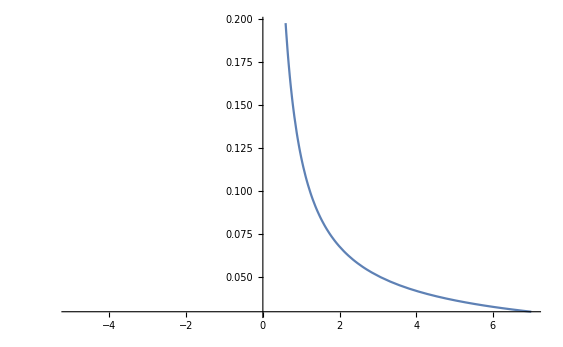

```mathematica
Plot[(√2 (1/r)^(3/2))/(3 π^2)+(√(1/r))/(√2 π^2),{r,-5.,7.}]
```

```mathematica
r*Sqrt[(√2 (1/r)^(3/2))/(3 π^2)+(√(1/r))/(√2 π^2)]
```

√((√(1/r))/(√2 π^2)+(√2 (1/r)^(3/2))/(3 π^2)) r

```mathematica
Simplify[√((√(1/r))/(√2 π^2)+(√2 (1/r)^(3/2))/(3 π^2)) r]
```

```mathematica
(r √((1/r)^(3/2) (2+3 r)))/(2^(1/4) √3 π)*4Pi
```

(2 2^(3/4) r √((1/r)^(3/2) (2+3 r)))/(√3)

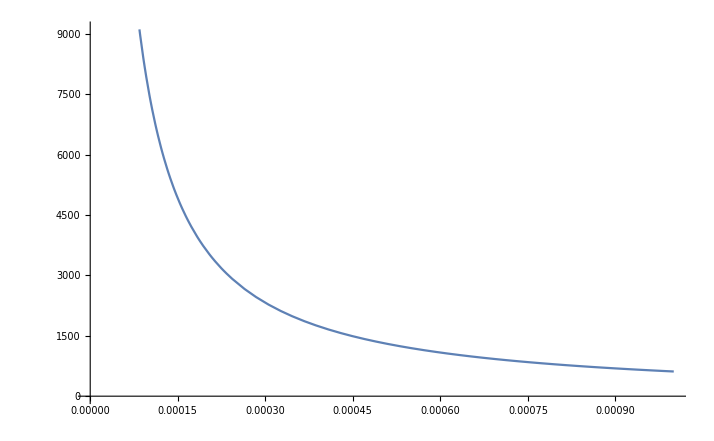

```mathematica
Plot[(1/r)E^((-2 2^(3/4) r √((1/r)^(3/2) (2+3 r)))/(√3)),{r,0,0.001}]
```

```mathematica
((Sqrt[u+(2/r)*E^((-2 2^(3/4) r √((1/r)^(3/2) (2+3 r)))/(√3))])^3)*HeavisideTheta[u+(2/r)*E^((-2 2^(3/4) r √((1/r)^(3/2) (2+3 r)))/(√3))]/(3Pi^2)
```

```mathematica
(1/r)E^(-0.1/r)
```

ⅇ^(-0.1/r)/r

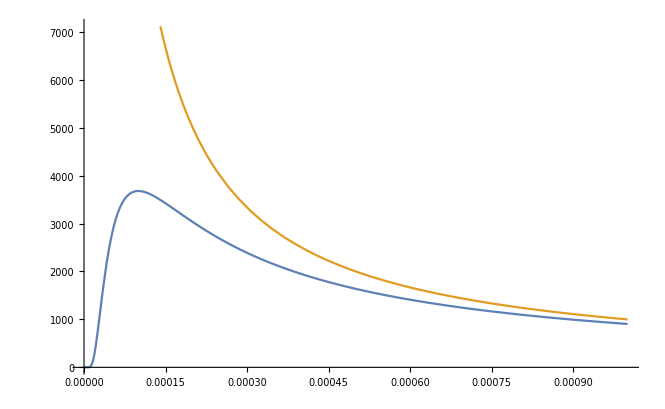

```mathematica
Plot[{ⅇ^(-0.0001/r)/r,1/r},{r,0,0.001}]
```

```mathematica
1/((r)^n+(a)^n)^(1/n)
```

(a^n+r^n)^(-1/n)

```mathematica
Limit[(0.1+r^n)^(-1/n),n->Infinity,r>0]
```

```mathematica
V[r_]=Limit[((0.1)^n+r^n)^(-1/n),n->∞,r>0]
```

Limit[(0.1^n+r^n)^(-1/n),n→∞,r>0]

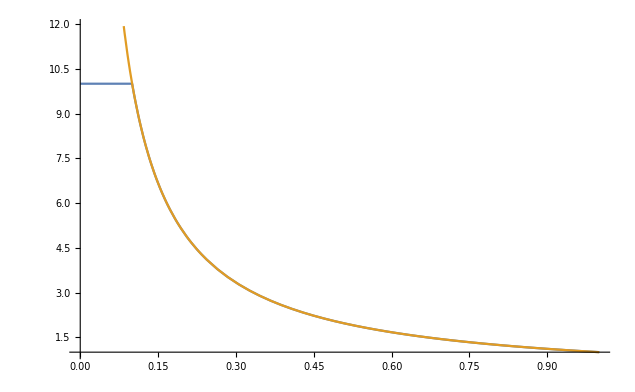

```mathematica
Plot[{V[r],1/r},{r,0,1}]
```

```mathematica
Plot[{Limit[(1+r^n)^(-1/n),n->∞,r>0],1/r}{r,0,1}]
```

```mathematica
Subscript[V, t][r_]=(E^(-0.1 r))/r
```

ⅇ^(-0.1 r)/r

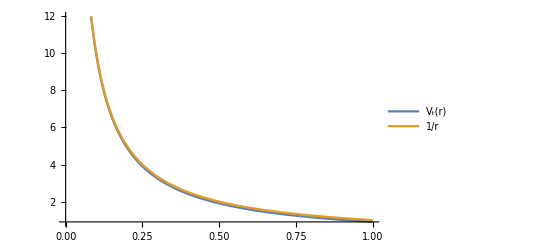

```mathematica
ⅇ^(-0.1 r)/r
Plot[{Subscript[V, t][r],1/r},{r,0,1},PlotLegends->"Expressions"]
```

```mathematica
Limit[(r^n+a^n)^(1/n),n->∞,{r>0,a>0}]
```

```mathematica
Limit[((a/r)^n+1^n)^(1/n),n->∞,{r>0,a>0}]
```

```mathematica
Subscript[V, L][r_,b_]=Log[E,b r+1]/r
```

Log[1+b r]/r

```mathematica
Manipulate[Plot[Log[a+r]/r,{r,0,0.1}],{a,1,2}]
```

```mathematica
Subscript[V, C][r_]=1/r
```

1/r

```mathematica
Manipulate[Plot[{Log[1+b r]/r,Subscript[V, C][r]},{r,0,10},PlotLegends->"Expressions"],{b,0,10}]
```

```mathematica
Log[10+r]/r
```

```mathematica
Log[1+10r]/r
```

Log[1+10 r]/r

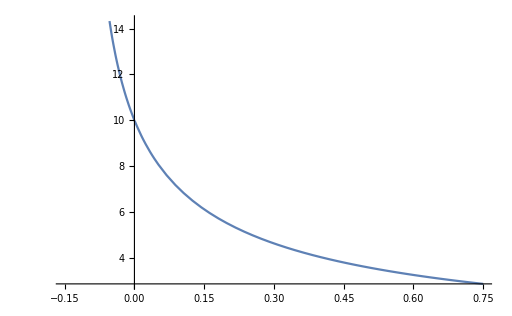

```mathematica
Plot[Log[1+10 r]/r,{r,-3/20,3/4}]
```

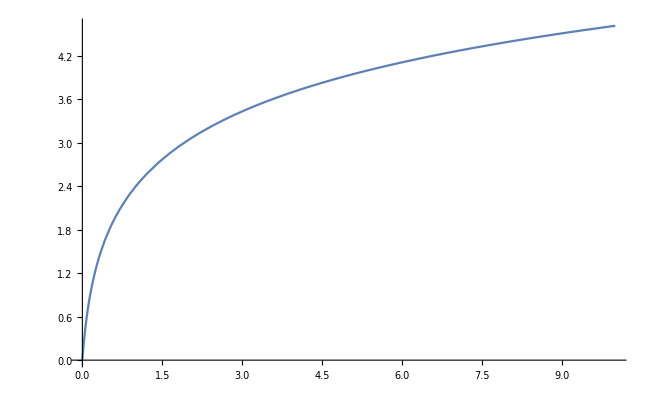

```mathematica
Plot[Log[1+10r],{r,0,10}]
```

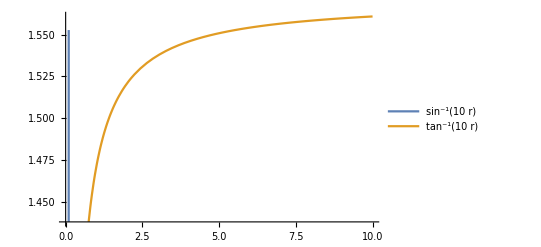

```mathematica
Plot[{ArcSin[10r],ArcTan[10r]},{r,0,10},PlotLegends->"Expressions"]
```

```mathematica
Subscript[V, AR][r_]=ArcTan[a r]/r
```

ArcTan[a r]/r

```mathematica
Manipulate[Plot[{ArcTan[a r]/r,Subscript[V, C][r]},{r,0,10.}],{a,-10,10}]
```

```mathematica
Subscript[V, E][r_]=(-1+a^r)/r
```

(-1+a^r)/r

```mathematica
Manipulate[Plot[(a^r-1)/r,{r,0.,1.}],{a,-10,100.}]
```

```mathematica
Manipulate[Plot[{(-1+a^r)/r,Subscript[V, C][r]},{r,0.,1}],{a,-10.,10.}]
```

```mathematica
Manipulate[Plot[{Limit[(b^n+r^n)^(-1/n),n->2],Subscript[V, C][r]},{r,0,1}],{b,0,1}]
```

```mathematica
Manipulate[Plot[{Limit[(b^n+r^n)^(-1/n),n->Infinity],Subscript[V, C][r]},{r,0,1}],{b,0,1}]
```

```mathematica
Manipulate[Plot[{1/(r+b),Subscript[V, C][r]},{r,0,1}],{b,0,1}]
```

```mathematica
Manipulate[Plot[Limit[(b^n+r^n)^(-1/n),n->Infinity],{r,0,2}],{b,0,1}]
```

```mathematica
1/(r ((b/r)^n+1)^(1/n))n∞
```